```mathematica
Solve[{(x-1)^2+y^2==2, (x+b)^2+y^2==2 b^2},{x,y}]
```

{{x→1/2 (-1+b),y→-1/2 √(-1+6 b-b^2)},{x→1/2 (-1+b),y→1/2 √(-1+6 b-b^2)}}

```mathematica
x->1/2 (-1+b)/. b->5
```

x→2

```mathematica
y->1/2 √(-1+6 b-b^2)/. b->5.828
```

y→0.0245764

```mathematica
Solve[0==1/2 √(-1+6 b-b^2)]
```

```mathematica
{{b->3-2 √2},{b->3+2 √2}}
```

```mathematica
3.+2 √2
```

5.82843

```mathematica
p={1/2 (-1+b),1/2 √(-1+6 b-b^2)}
```

{1/2 (-1+b),1/2 √(-1+6 b-b^2)}

```mathematica
v1={1,0}-p
v2={-b,0}-p
```

{1+(1-b)/2,-1/2 √(-1+6 b-b^2)}

{(1-b)/2-b,-1/2 √(-1+6 b-b^2)}

```mathematica
α= ArcCos[(v1.v2)/(Norm[v1] Norm[v2])]
```

ArcCos[((1+(1-b)/2) ((1-b)/2-b)+1/4 (-1+6 b-b^2))/(√(Abs[1+(1-b)/2]^2+1/4 Abs[-1+6 b-b^2]) √(Abs[(1-b)/2-b]^2+1/4 Abs[-1+6 b-b^2]))]

```mathematica
α /. b->10
```

ArcCos[9/(7 √5)]

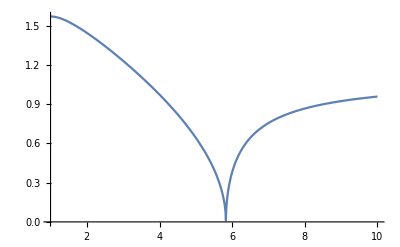

```mathematica
Plot[α,{b,1,10}]
```

```mathematica
Solve[-b+√2 b==1+√2]
```

{{b→(1+√2)/(-1+√2)}}

```mathematica
Simplify[(1+√2)/(-1+√2)]
```

3+2 √2